#### A collection of challenging elastic maps T for finding the closest-Sigma-to-T. The issues pertain to using the built-in Mathematica function NMinimize. ES_FindSymGroups.nb calls GetTempAndθ0σ0ϕ0, which calls NMinimize. Here we experiment with different options for GetTempAndθ0σ0ϕ0. INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, chooseTmat.nb, then this notebook

## General functions

```mathematica
WantDetails="WantDetails";
```

#### Function to minimize over a square patch

```mathematica
Flocal[theta0_,phi0_,dtheta_,dphi_,Tmat_]:=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],theta0-dtheta≤θ≤theta0+dtheta&&phi0-dphi≤ϕ≤phi0+dphi},{θ,ϕ},Method->"RandomSearch"]
```

#### 2D Search for the closest MONO map to Tmat

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

## Example 1: Brown map, 2D search with θ_max = π

```mathematica
Tmat = TmatBrown;
```

#### The problematic point is the closest MONO to closestMONO (dt = 0.5). By definition, the closest MONO to closestMONO should have β = 0, but it does not. This impacts the trajectory from MONO to ORTH as well.

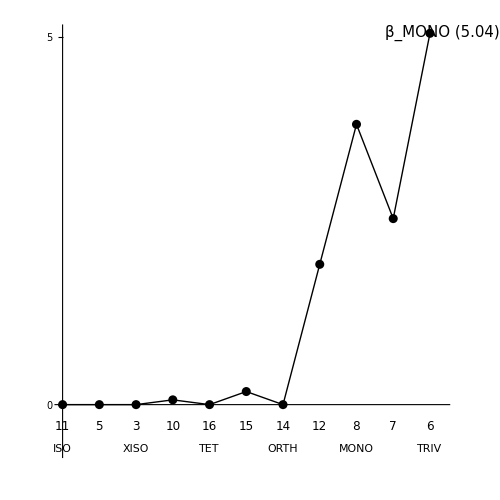

#### Adjust dθ based on how close the local minima are.

```mathematica
dtheta = 0.2π;
dphi=dtheta;
```

#### 2D search with θ_max = π

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

#### Closest MONO map to the input TRIV map:

```mathematica
OutputFor[Tmat,MONO]
```

#### CORRECT MINIMUM (d = 26.7661): Upper left blue patch (green point) and its antipode region:

```mathematica
Flocal[0.5π,0.75π,dtheta,dphi,Tmat]
Flocal[1.5π,0.3π,dtheta,dphi,Tmat]
```

#### LOCAL MINIMUM (d = 27.6842): Central blue patch and its antipode region:

```mathematica
Flocal[π,0.5π,dtheta,dphi,Tmat]
Flocal[0.,0.5π,dtheta,dphi,Tmat]
```

#### LOCAL MINIMUM (d = 27.387): Lower left blue patch and its antipode region:

```mathematica
Flocal[0.4 π,0.2π,dtheta,dphi,Tmat]
Flocal[1.4π,0.8π,dtheta,dphi,Tmat]
```

#### The full search finds the right minimum (as before):

```mathematica
Flocal[π,0.5π,π,0.5π,Tmat]
```

#### Problematic map.

```mathematica
TmatMONO=Closest[Tmat,MONO];
MatrixForm[TmatMONO]
```

#### This gives the wrong minimum:

```mathematica
OutputFor[TmatMONO,MONO]
```

```mathematica
βT[TmatMONO,MONO]/Degree
```

#### CORRECT MINIMUM (d ~ 0): Upper left blue patch and its antipode region:

```mathematica
Flocal[0.5π,0.75π,dtheta,dphi,TmatMONO]
Flocal[1.5π,0.3π,dtheta,dphi,TmatMONO]
```

#### INCORRECT MINIMUM (d = 20.1386): Central blue patch and its antipode region:

```mathematica
Flocal[π,0.5π,dtheta,dphi,TmatMONO]
Flocal[0.,0.5π,dtheta,dphi,TmatMONO]
```

#### LOCAL MINIMUM (d = 20.1386): Lower left blue patch (green dot) and its antipode region:

```mathematica
Flocal[0.4 π,0.2π,dtheta,dphi,TmatMONO]
Flocal[1.4π,0.8π,dtheta,dphi,TmatMONO]
```

#### By extending the θ search range slightly, the 2D search finds the correct minimum:

```mathematica
fac=1.15; (* NMinimize fails *)
fac=1.2; (* NMinimize works *)
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤fac π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
OutputFor[TmatMONO,MONO]
```

```mathematica
βT[TmatMONO,MONO]/Degree
```

#### The 3D search finds the correct minimum (d ~ 0):

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]= NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],MONO],0≤θ≤2π&&-π≤σ≤π&&0≤ϕ≤π},{θ,σ,ϕ},Method->"RandomSearch"];
{θ0,σ0,ϕ0}=({θ,σ,ϕ}/.temp[Tmat,MONO][[2]]);)
OutputFor[TmatMONO,MONO]
```

## Example 2: Brown map, 2D search with θ_max = 2π

```mathematica
Tmat = TmatBrown;
```

#### The problematic point is between TET and XISO (dt =0.2):

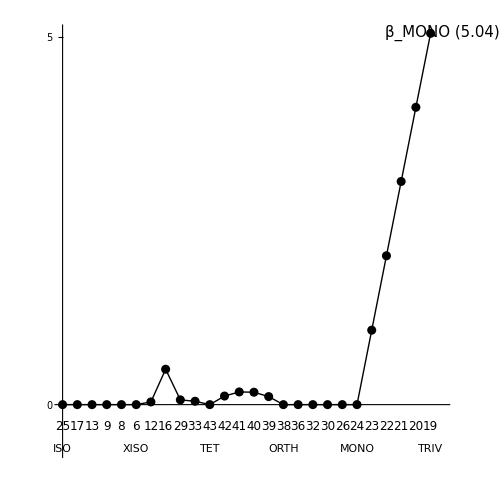

#### Adjust dθ based on how close the local minima are.

```mathematica
dtheta = 0.2π; dphi=dtheta;
```

#### 2D search with θ_max = 2π

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤2π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

#### Check the starting value of TRIV (beta = 5.04)

```mathematica
OutputFor[Tmat,MONO]
```

#### Get the closest TET and closest XISO

```mathematica
OutputFor[Tmat,TET]
OutputFor[Tmat,XISO]
```

#### Reconstruct the problematic map. For the dt = 0.2 lattice, this is a point between 43 (TET) and 6 (XISO): 43 (TET), 33, 29, 16*, 12, 6 (XISO)

```mathematica
TmatTET=Closest[Tmat,TET];
TmatXISO=Closest[Tmat,XISO];
Tmatx=0.4TmatTET+0.6TmatXISO;
MatrixForm[TmatTET]
MatrixForm[TmatXISO]
MatrixForm[Tmatx]
```

#### This fails to find the global minimum:

```mathematica
OutputFor[Tmatx,MONO]
```

```mathematica
βT[Tmatx,MONO]/Degree
```

#### CORRECT MINIMUM (d = 0.299): blue patch near θ = 0

```mathematica
Flocal[π,0.5π,dtheta,dphi,Tmatx]
Flocal[0,0.5π,dtheta,dphi,Tmatx]
```

#### INCORRECT MINIMUM (d = 2.398): blue path near θ = pi/2

```mathematica
Flocal[0.5π,0.5π,dtheta,dphi,Tmatx]
Flocal[1.5π,0.5π,dtheta,dphi,Tmatx]
```

#### LOCAL MINIMUM (d = 2.416): blue patch near poles

```mathematica
Flocal[0.7π,0.9π,dtheta,dphi,Tmatx]
Flocal[1.7π,0.1π,dtheta,dphi,Tmatx]
```

#### Change the θ search range to π, and then it finds the global minimum:

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

```mathematica
OutputFor[Tmatx,MONO]
```

```mathematica
βT[Tmatx,MONO]/Degree
```

#### Change to a 3D search, and then it finds the global minimum:

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]= NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],MONO],0≤θ≤2π&&-π≤σ≤π&&0≤ϕ≤π},{θ,σ,ϕ},Method->"RandomSearch"];
{θ0,σ0,ϕ0}=({θ,σ,ϕ}/.temp[Tmat,MONO][[2]]);)
```

```mathematica
OutputFor[Tmatx,MONO]
```

## Example 3: Igel map, 2D search with θ_max = 2π

```mathematica
Tmat = TmatIgel;
```

#### The problematic point is between TRIV and MONO (dt = 0.2):

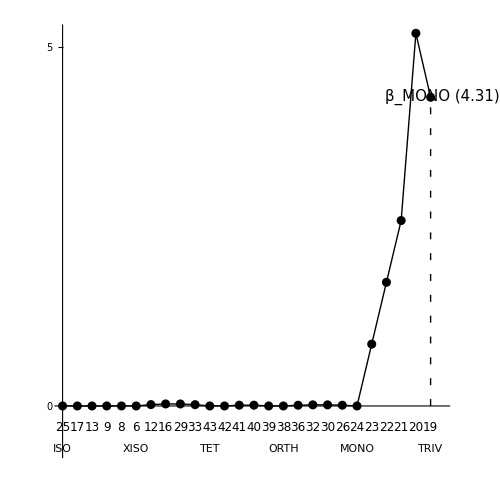

```mathematica
dtheta = 0.1π;
dphi=dtheta;
```

#### 2D search with θ_max = 2π

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤2π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

#### Closest MONO map to the input TRIV map:

```mathematica
OutputFor[Tmat,MONO]
```

#### Now we start with the MONO map closest to our initial map. Same as the 6x6 matrix above:

```mathematica
TmatMONO=Closest[Tmat,MONO];
MatrixForm[TmatMONO]
```

#### Reconstruct the problematic map: between Tmat and TmatMONO (mostly Tmat).

```mathematica
Tmatx=0.8Tmat+0.2TmatMONO;
```

```mathematica
OutputFor[Tmatx,MONO]
```

```mathematica
βT[Tmatx,MONO]/Degree
```

#### The green dot in the contour plot turns out to be a local minimum, as we see next.

#### CORRECT MINIMUM (d = 1.419): blue patch at the center and its antipode region:

```mathematica
Flocal[π,0.5π,dtheta,dphi,Tmatx]
Flocal[0,0.5π,dtheta,dphi,Tmatx]
```

#### INCORRECT MINIMUM (d = 2.138): blue patch (with green dot) to the upper left of center:

```mathematica
Flocal[0.8 π,0.6π,dtheta,dphi,Tmatx]
```

#### Change the search range back to π, and it works:

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

```mathematica
OutputFor[Tmatx,MONO]
```

```mathematica
βT[Tmatx,MONO]/Degree
```

#### Change to a 3D search, and then it finds the global minimum:

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]= NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],MONO],0≤θ≤2π&&-π≤σ≤π&&0≤ϕ≤π},{θ,σ,ϕ},Method->"RandomSearch"];
{θ0,σ0,ϕ0}=({θ,σ,ϕ}/.temp[Tmat,MONO][[2]]);)
```

```mathematica
OutputFor[Tmatx,MONO]
```

## Example 4: TmatMar17 map, 2D search with θ_max = π

```mathematica
Tmat = TmatMar17;
```

#### The problematic point is between ORTH and TET (dt =0.2, θ_max = π):

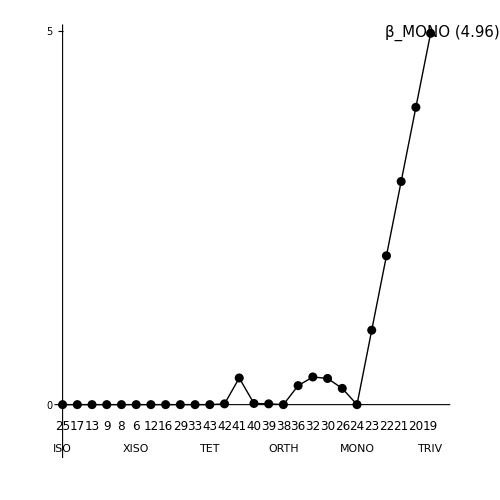

#### Adjust dθ based on how close the local minima are.

```mathematica
dtheta = 0.2π; dphi=dtheta;
```

#### 2D search with θ_max = π

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

#### Check the starting value of TRIV (β_MONO= 4.96)

```mathematica
OutputFor[Tmat,MONO]
```

#### LOCAL MINIMUM (d = 75.48): blue sausage near θ = 2π

```mathematica
Flocal[1.95π,0.5π,dtheta,dphi,Tmat]
Flocal[0.95 π,0.5π,dtheta,dphi,Tmat]
```

#### CORRECT MINIMUM (d = 64.42): blue sausage (green dot) near θ = π/2

```mathematica
Flocal[0.5π,0.5π,dtheta,dphi,Tmat]
Flocal[1.5π,0.5π,dtheta,dphi,Tmat]
```

#### LOCAL MINIMUM (d = 80.88): blue isolated patch

```mathematica
Flocal[0.4π,0.2π,dtheta,dphi,Tmat]
```

#### Get the closest ORTH and TET

```mathematica
OutputFor[Tmat,ORTH]
OutputFor[Tmat,TET]
```

#### Reconstruct the problematic map.

```mathematica
TmatORTH=Closest[Tmat,ORTH];
TmatTET=Closest[Tmat,TET];
Tmatx=0.6TmatTET+0.4TmatORTH;
MatrixForm[TmatORTH]
MatrixForm[TmatTET]
MatrixForm[Tmatx]
```

#### This fails to find the global minimum (it finds β = 0.356^o, but the minimum is β = 0.015^o):

```mathematica
OutputFor[Tmatx,MONO]
```

```mathematica
βT[Tmatx,MONO]/Degree
```

#### LOCAL MINIMUM (d = 4.572): blue sausage near θ = 2π

```mathematica
Flocal[1.95π,0.5π,dtheta,dphi,Tmatx]
Flocal[0.95 π,0.5π,dtheta,dphi,Tmatx]
```

#### INCORRECT MINIMUM (d = 4.569): blue sausage near θ = π/2

```mathematica
Flocal[0.5π,0.5π,dtheta,dphi,Tmatx]
Flocal[1.5π,0.5π,dtheta,dphi,Tmatx]
```

#### CORRECT MINIMUM (d = 0.197): blue isolated patch

```mathematica
Flocal[0.4π,0.2π,dtheta,dphi,Tmatx]
```

#### Change the θ search range to 2π, and then it finds the global minimum:

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0.05≤θ≤2π+0.05&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[Tmat,MONO][[2,1]];
σ0=0;
ϕ0=ϕ/.temp[Tmat,MONO][[2,2]];)
```

```mathematica
OutputFor[Tmatx,MONO]
```

```mathematica
βT[Tmatx,MONO]/Degree
```

#### Change to a 3D search, and then it finds the global minimum:

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(Clear[θ,σ,ϕ];
temp[Tmat,MONO]= NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],MONO],0≤θ≤2π&&-π≤σ≤π&&0≤ϕ≤π},{θ,σ,ϕ},Method->"RandomSearch"];
{θ0,σ0,ϕ0}=({θ,σ,ϕ}/.temp[Tmat,MONO][[2]]);)
```

```mathematica
OutputFor[Tmatx,MONO]
```